```mathematica
SetDirectory@NotebookDirectory[];
Import["esmlib_nsl.wl"]
```

```mathematica
eq1=i1==i2+i3;
eqn2s={
i1==(v[j-1,t]-v[j,t])/r,
i2==(v[j,t]-v[j+1,t])/r,
i3==c D[v[j,t],t]
}
```

{i1==(v[-1+j,t]-v[j,t])/r,i2==(v[j,t]-v[1+j,t])/r,i3==c v^(0,1)[j,t]}

```mathematica
Simplify[Eliminate[Append[eqn2s,eq1],{i1,i2,i3}],Assumptions->r≠0]
sol=Equal@@(Solve[%,D[v[j,t],t]][[1,1]]);
sol//TraditionalForm
```

v[-1+j,t]+v[1+j,t]==2 v[j,t]+c r v^(0,1)[j,t]

v^(0,1)(j,t)==(v(j-1,t)-2 v(j,t)+v(j+1,t))/(c r)

```mathematica
Expand@sol
```

v^(0,1)[j,t]==v[-1+j,t]/(c r)-(2 v[j,t])/(c r)+v[1+j,t]/(c r)

```mathematica
NDSolve[{sol/.j->0,v[0,0]==0},v,{t,0,10}]
```

NDSolve::underdet: There are more dependent variables, {v[-1,t],v[0,t],v[1,t]}, than equations, so the system is underdetermined.

NDSolve[{v^(0,1)[0,t]==(v[-1,t]-2 v[0,t]+v[1,t])/(c r),v[0,0]==0},v,{t,0,10}]

# Matrix version

```mathematica
n=100;
tmax=10;
```

```mathematica
ones=DiagonalMatrix[Table[1,n-1],1];
a=ones+Transpose@ones+DiagonalMatrix[Table[-2,n]];
(*a[[{1,n},All]]=0;
a[[All,{1,n}]]=0;*)
a//MatrixForm;
```

```mathematica
vals=N[Eigenvalues[n^2*a]/Pi^2]
```

{-4051.87,-4048.93,-4044.03,-4037.18,-4028.39,-4017.66,-4005.,-3990.43,-3973.96,-3955.61,-3935.38,-3913.32,-3889.42,-3863.73,-3836.25,-3807.03,-3776.08,-3743.44,-3709.14,-3673.21,-3635.69,-3596.61,-3556.01,-3513.94,-3470.42,-3425.51,-3379.24,-3331.66,-3282.83,-3232.77,-3181.55,-3129.21,-3075.81,-3021.39,-2966.,-2909.71,-2852.56,-2794.62,-2735.93,-2676.55,-2616.55,-2555.97,-2494.88,-2433.34,-2371.41,-2309.14,-2246.6,-2183.84,-2120.94,-2057.94,-1994.91,-1931.91,-1869.,-1806.25,-1743.71,-1681.44,-1619.5,-1557.96,-1496.87,-1436.3,-1376.29,-1316.92,-1258.23,-1200.28,-1143.14,-1086.84,-1031.46,-977.041,-923.635,-871.297,-820.076,-770.022,-721.183,-673.607,-627.34,-582.427,-538.91,-496.833,-456.235,-417.156,-379.634,-343.706,-309.405,-276.765,-245.819,-216.594,-189.121,-163.425,-139.531,-117.463,-97.2418,-78.8868,-62.4159,-47.845,-35.1883,-24.458,-15.6645,-8.81626,-3.91992,-0.980217}

```mathematica
vecs=N@Eigenvectors[n^2*a];
```

```mathematica
Manipulate[ListLinePlot[vecs[[i]]],{{i,n},1,n,1}]
```

```mathematica
(*FullSimplify@Eigenvalues[n^2*a]*)
```

```mathematica
initial=Table[1,n];initial[[{1,n}]]=0;
dsol=NDSolve[{v'[t]==a.v[t],v[0]==initial},v,{t,0,tmax}][[1]]
```

{v→InterpolatingFunction[{{0., 10.}}, <>]}

```mathematica
ClearAll[vfunc]
vfunc[j_,t_?NumberQ]:=(v/.dsol)[t][[j]]
```

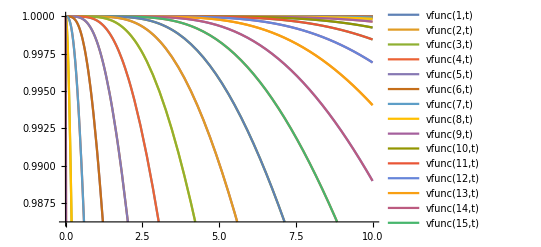

```mathematica
Plot[Evaluate@Quiet@Table[vfunc[j,t],{j,1,n}],{t,0,tmax},PlotLegends->"Expressions"]
```

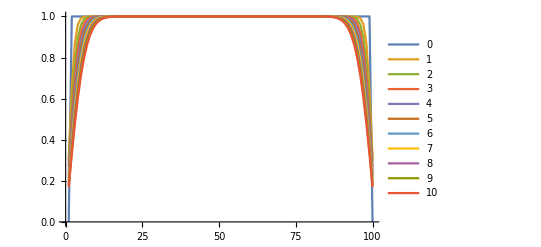

```mathematica
tvals=Range[0,tmax,Round[tmax/10]];
ListLinePlot[Evaluate@Quiet@Table[vfunc[j,t],{t,tvals},{j,n}],PlotLegends->tvals]
```